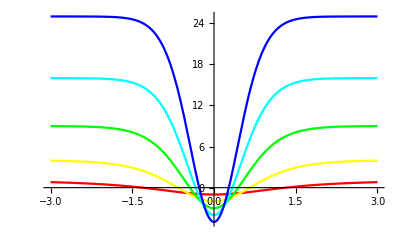

```mathematica
Color = {Red, Yellow, Green, Cyan, Blue, Purple};
f = σ^2 - σ*(σ + 1)*Sech[x]^σ;
ff = Table[f, {σ, 1, 5, 1}];
Plot[ff, {x, -3, 3}, PlotRange -> All, PlotStyle ->  Color]
```

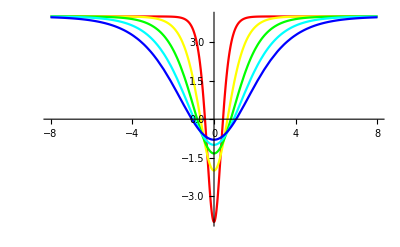

```mathematica
a = 4 - (4*(1+σ))/σ*Sech[(2*x)/σ]^2;
aa = Table[a, {σ, 1,5,1}];
Plot[aa, {x, -8,8}, PlotRange-> All, PlotStyle -> Color]
```

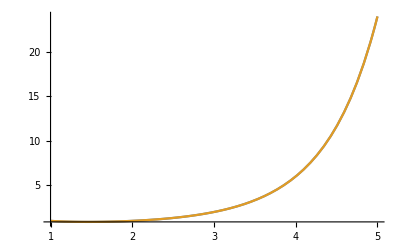

```mathematica
Plot[{Gamma[x], Gamma[x,0]}, {x, 1,5}, PlotRange-> All]
```

```mathematica
Gamma[0]
```

ComplexInfinity

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
Integrate[x^(z-1)*Exp[x], x]
```

-(-x)^-z x^z Gamma[z,-x]

```mathematica
Integrate[Integrate[x^2,x],x]
```

x^4/12

```mathematica
Expand[Integrate[Gamma[x],x]]
```

∫Gamma[x]ⅆx

```mathematica
Gamma[1,0] == Gamma[1]
```

True

```mathematica
N[Gamma[1,0]]
```

1.

```mathematica
Gamma[1]
```

1

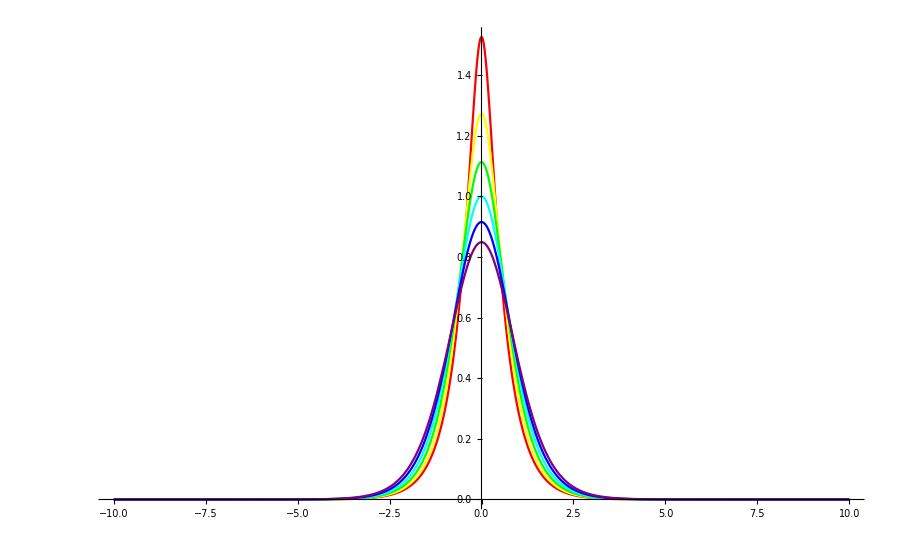

```mathematica
Subscript[ψ, 0]= (4*Gamma[(1+σ)/2])/(√π*σ*Gamma[σ/2])*Sech[(2*x)/σ]^(σ);
ψ = Table[Subscript[ψ, 0], {σ, 0.5,3,0.5}];
Plot[ψ,{x,-10,10}, PlotRange-> All, PlotStyle-> Color, ImageSize-> 900]
```

```mathematica
LinearGradientImage["Rainbow"]
```

-Graphics-

```mathematica
Gradient
```

Gradient